## Practise 8: group 2. Nerea Andia, Ander Cano, Mikel Lamela and Aitor Larrinoa.

## 8.1. Galerkin Method

### a) Write a program in Mathematica that solves (8.5) using Galerkin method and compares the approximated solution with the exact one

```mathematica
Clear["Global`*"]
n=10;
fun[y_] := y;
k[y_] := 1+y;
u0= 0;
vsin[ k_,y_] := Sin[k  Pi y]
```

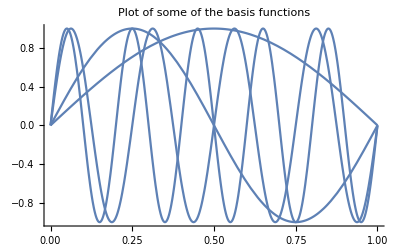

```mathematica
For[ i=1,i≤n, i++,grafico[i]=Plot[vsin[i,y],{y,0,1},PlotRange->All]]
Show[grafico[2],grafico[1],grafico[n-2],grafico[n],PlotLabel->"Plot of some of the basis functions"]
```

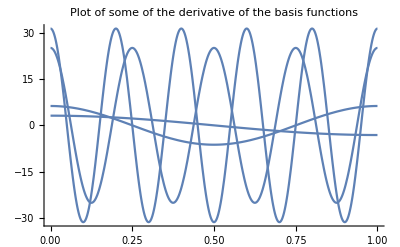

```mathematica
dvsin[j_,y_]=D[vsin[j,y],y];
For[ i=1,i≤n, i++,grafico[i]=Plot[dvsin[i,y],{y,0,1},PlotRange->All]]
Show[grafico[1],grafico[2],grafico[n-2],grafico[n],PlotLabel->"Plot of some of the derivative of the basis functions"]
```

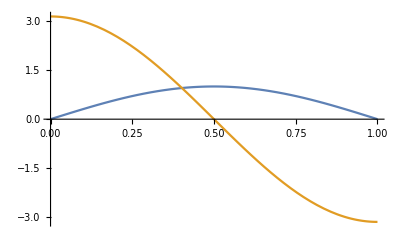

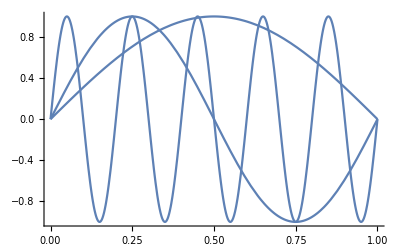

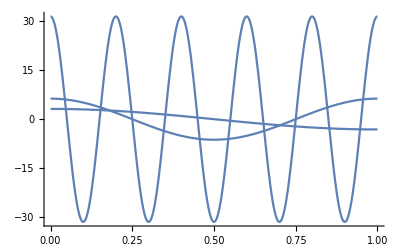

```mathematica
For[ j=1,j≤ n, j++,v[j_,y_] := vsin[j,y]/;  Mod[j,1]==0]
For[ j=1,j≤ n, j++,dv[j_,y_] := dvsin[j,y]/;  Mod[j,1]==0]
Plot[{v [1,y],dv[1,y]},{y,0,1},PlotRange->Full]
For[ i=1,i≤ n, i++,grafico[i]=Plot[v[i,y],{y,0,1},PlotRange->All]]
Show[grafico[1],grafico[2],grafico[n]]
For[ i=1,i≤ n, i++,grafico[i]=Plot[dv[i,y],{y,0,1},PlotRange->All]]
Show[grafico[1],grafico[2],grafico[n]]
```

```mathematica
Do[ a[i,j] = N[∫_0^1 k[x]*dv[j,x]  dv[i,x]ⅆx ],{i,n},{j,n}]
AA = Table[a[i,j],{i,n},{j,n}];
MatrixForm[%];
Det[AA];
Do[ b[j] =N[∫_0^1 fun[x] v[j,x]ⅆx],{j,n}]
ff=Array[b,n];
MatrixForm[%];
```

```mathematica
u = N[LinearSolve[AA, ff]];
Solution [y_] := ∑_(k=1)^n u[[k]] v[k,y];

Uexact[y_]:= y/2-y^2/4-Log[1+y]/(4*Log[2]);
```

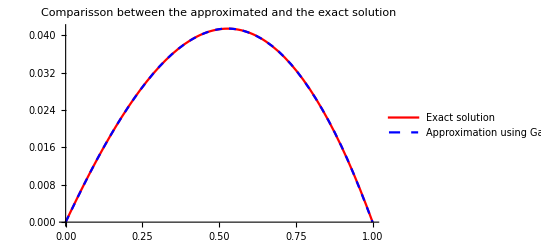

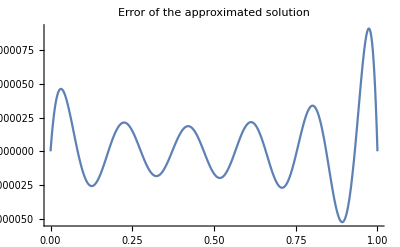

```mathematica
Plot[{Uexact[y],Solution[y]},{y,0,1}, PlotStyle->{Red, {Blue, Dashed}}, PlotLabel-> "Comparisson between the approximated and the exact solution",PlotLegends->{"Exact solution","Approximation using Galerkin"}]
Plot[{Uexact[y]-Solution[y]},{y,0,1},PlotRange->All, PlotLabel-> "Error of the approximated solution"]
```

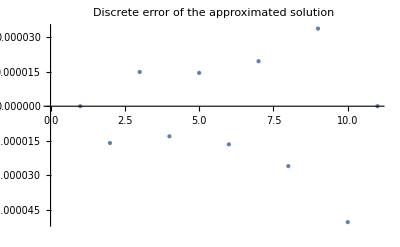

```mathematica
(*discrete error*)
ListPlot[Table[Uexact[y]-Solution[y],{y,0,1,1/n}],PlotStyle->PointSize[Large], PlotLabel-> "Discrete error of the approximated solution"]
```

```mathematica
(*max value discrete error*)
Max[Table[Abs[Uexact[y]-Solution[y]],{y,0,1,1/n}]]
```

0.000050303

```mathematica
ScientificForm[0.000050302992449541284]
```

5.0303×10^-5

### b)Write a program that solves (5.2), using Galerkin method and with two different f(x). Compare the approximated solutions with the ones obtained using FD method for elliptic problems.

#### f(x) = (3x+x^2)exp(x)

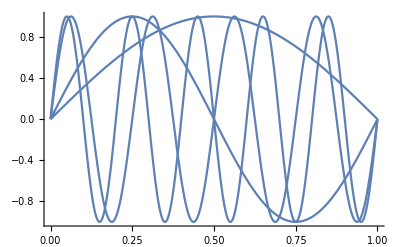

```mathematica
Clear["Global`*"]
tgal0=TimeUsed[];
n=10;

fun[y_] := (3y+y^2)*Exp[y];
k[y_] := 1;
u0= 0;
vsin[ k_,y_] := Sin[k  Pi y] 
For[ i=1,i≤n, i++,grafico[i]=Plot[vsin[i,y],{y,0,1},PlotRange->All]]
Show[grafico[2],grafico[1],grafico[n-2],grafico[n]]
```

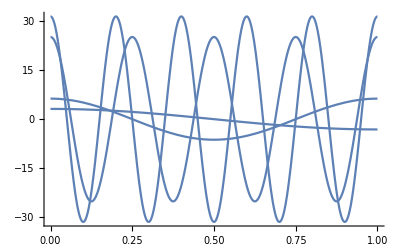

```mathematica
dvsin[j_,y_]=D[vsin[j,y],y];
For[ i=1,i≤n, i++,grafico[i]=Plot[dvsin[i,y],{y,0,1},PlotRange->All]]
Show[grafico[1],grafico[2],grafico[n-2],grafico[n]]
```

```mathematica
For[ j=1,j≤ n, j++,v[j_,y_] := vsin[j,y]/;  Mod[j,1]==0]
For[ j=1,j≤ n, j++,dv[j_,y_] := dvsin[j,y]/;  Mod[j,1]==0]
Plot[{v [1,y],dv[1,y]},{y,0,1},PlotRange->Full]
For[ i=1,i≤ n, i++,grafico[i]=Plot[v[i,y],{y,0,1},PlotRange->All]]
Show[grafico[1],grafico[2],grafico[n]]
```

-Graphics-

-Graphics-

```mathematica
For[ i=1,i≤ n, i++,grafico[i]=Plot[dv[i,y],{y,0,1},PlotRange->All]]
Show[grafico[1],grafico[2],grafico[n]]
```

-Graphics-

```mathematica
Do[ a[i,j] = N[∫_0^1 k[x]*dv[j,x]  dv[i,x]ⅆx ],{i,n},{j,n}]
AA = Table[a[i,j],{i,n},{j,n}];
MatrixForm[%];
Det[AA];
Do[ b[j] =N[∫_0^1 fun[x] v[j,x]ⅆx],{j,n}]
ff=Array[b,n];
MatrixForm[%];
```

```mathematica
u=N[LinearSolve[AA, ff]];
Solution [y_] := ∑_(k=1)^n u[[k]] v[k,y];
```

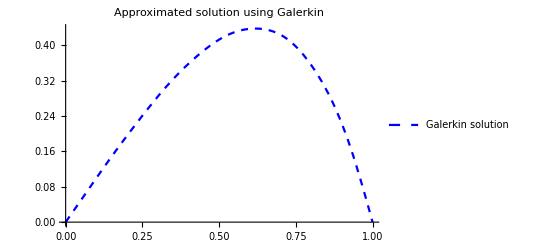

```mathematica
(*plot the solution using the Galerkin method:*)
pGAL=Plot[{Solution[y]},{y,0,1}, PlotStyle->{Blue, Dashed}, PlotLabel-> "Approximated solution using Galerkin",PlotLegends->{"Galerkin solution"}]
```

```mathematica
tgal1=TimeUsed[];
tgal=tgal1-tgal0
```

28.5

We calculate the exact solution and we compare both solutions

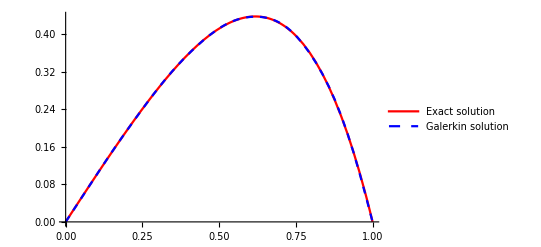

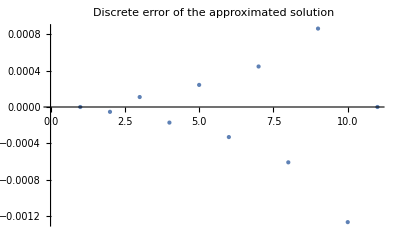

0.00126504

```mathematica
sol=DSolve[{-u1''[x]==fun[x],u1[0]==0,u1[1]==0},u1[x],x];
Uexact[x_]:=-ⅇ^x (-1+x) x;
p0=Plot[Evaluate[u1[x]/.sol],{x,0,1},PlotStyle->Red,PlotLegends->{"Exact solution"}];
Show[p0,pGAL]
ListPlot[Table[Uexact[y]-Solution[y],{y,0,1,1/n}],PlotStyle->PointSize[Large], PlotLabel-> "Discrete error of the approximated solution"] (*Error*)
(*max value discrete error*)
Max[Table[Abs[Uexact[y]-Solution[y]],{y,0,1,1/n}]]
(*approximated solution using the FD method:*)
tfd0=TimeUsed[];
```

We calculate the approximated solution usinf the FD method

```mathematica
M = 20;
Δx= 1/(M+1);
xx[j_]:= j Δx;
BB:= BB=Table[fun[xx[i]] ,{i,M}]; A:= A=SparseArray[{i_,j_}/;i==j+1->-1,{M,M}] + SparseArray[{i_,j_}/;i==j-1->-1,{M,M}] + SparseArray[{i_,j_}/;i==j->2,{M,M}]//Normal
Anew = A / (Δx^2);
XX=Table[X[j],{j,M}] ; 
Sol1 = Solve[Anew. XX == BB, XX];
XX1 = Flatten[XX /. Sol1];
XX1 = Prepend[XX1,0]; 
XX1 = Append[XX1,0];
pFD=ListPlot[Table[{Δx j, XX1[[j+1]]},{j,0,M+1}], Joined-> True, PlotRange-> All, AxesLabel -> {"x", " "},PlotStyle->Green,PlotLegends->{"FD approximation"}];

tfd1=TimeUsed[];
tfd=tfd1-tfd0;
```

We compare both solutions

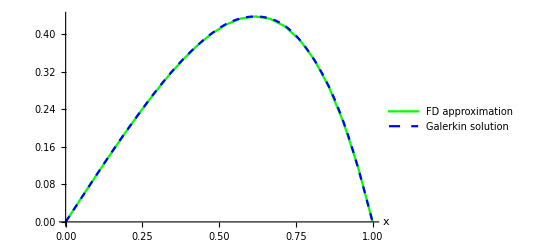

28.5

0.11

```mathematica
Show[pFD,pGAL]
tgal
tfd
```

#### f(x) = sin(x)exp(x)

```mathematica
Clear["Global`*"]
tgal0=TimeUsed[];
n=10;

fun[y_] := Sin[y]*Exp[y];
k[y_] := 1;
u0= 0;
vsin[ k_,y_] := Sin[k  Pi y]
```

```mathematica
For[ i=1,i≤n, i++,grafico[i]=Plot[vsin[i,y],{y,0,1},PlotRange->All]]
Show[grafico[2],grafico[1],grafico[n-2],grafico[n]]
dvsin[j_,y_]=D[vsin[j,y],y];
For[ i=1,i≤n, i++,grafico[i]=Plot[dvsin[i,y],{y,0,1},PlotRange->All]]
Show[grafico[1],grafico[2],grafico[n-2],grafico[n]]
```

```mathematica
For[ j=1,j≤ n, j++,v[j_,y_] := vsin[j,y]/;  Mod[j,1]==0]
For[ j=1,j≤ n, j++,dv[j_,y_] := dvsin[j,y]/;  Mod[j,1]==0]
Plot[{v [1,y],dv[1,y]},{y,0,1},PlotRange->Full]
For[ i=1,i≤ n, i++,grafico[i]=Plot[v[i,y],{y,0,1},PlotRange->All]]
Show[grafico[1],grafico[2],grafico[n]]
```

```mathematica
For[ i=1,i≤ n, i++,grafico[i]=Plot[dv[i,y],{y,0,1},PlotRange->All]]
Show[grafico[1],grafico[2],grafico[n]]
```

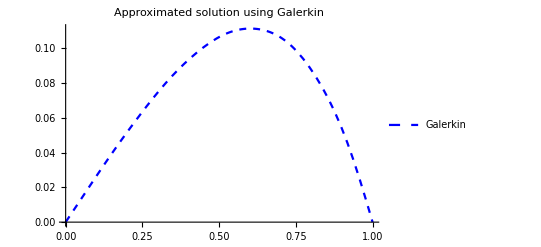

```mathematica
Do[ a[i,j] = N[∫_0^1 k[x]*dv[j,x]  dv[i,x]ⅆx ],{i,n},{j,n}]
AA = Table[a[i,j],{i,n},{j,n}];
MatrixForm[%];
Det[AA];
Do[ b[j] =N[∫_0^1 fun[x] v[j,x]ⅆx],{j,n}]
ff=Array[b,n];
MatrixForm[%];
u = N[LinearSolve[AA, ff]];
Solution [y_] := ∑_(k=1)^n u[[k]] v[k,y];
pGAL=Plot[{Solution[y]},{y,0,1}, PlotStyle->{Blue, Dashed}, PlotLabel-> "Approximated solution using Galerkin",PlotLegends->{"Galerkin"}]
tgal1=TimeUsed[];
tgal=tgal1-tgal0;
```

We calculate the exact solution and compare it with Galerkin

{{u1[x]→1/2 (-1+x-ⅇ x Cos[1]+ⅇ^x Cos[x])}}

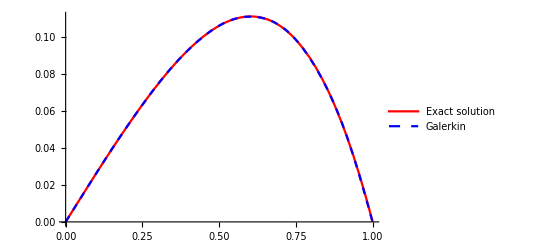

```mathematica
sol=DSolve[{-u1''[x]==fun[x],u1[0]==0,u1[1]==0},u1[x],x]
Uexact[x_]:=1/2 (-1+x-ⅇ x Cos[1]+ⅇ^x Cos[x]);
p0=Plot[Evaluate[u1[x]/.sol],{x,0,1},PlotStyle->Red,PlotLegends->{"Exact solution"}];
Show[p0,pGAL]
```

We attend to the error

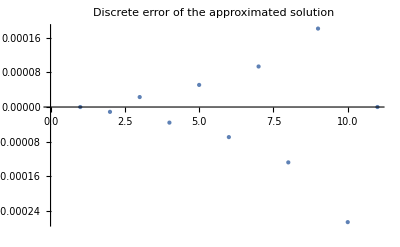

0.00026656

```mathematica
ListPlot[Table[Uexact[y]-Solution[y],{y,0,1,1/n}],PlotStyle->PointSize[Large], PlotLabel-> "Discrete error of the approximated solution"] (*Error*)
(*max value discrete error:*)
Max[Table[Abs[Uexact[y]-Solution[y]],{y,0,1,1/n}]]
```

We calculate the approximated solution using FD method

```mathematica
tfd0=TimeUsed[];
M = 20;
Δx= 1/(M+1);
xx[j_]:= j Δx;
BB:= BB=Table[fun[xx[i]] ,{i,M}]; A:= A=SparseArray[{i_,j_}/;i==j+1->-1,{M,M}] + SparseArray[{i_,j_}/;i==j-1->-1,{M,M}] + SparseArray[{i_,j_}/;i==j->2,{M,M}]//Normal
Anew = A / (Δx^2);
XX=Table[X[j],{j,M}] ; 
Sol1 = Solve[Anew. XX == BB, XX];
XX1 = Flatten[XX /. Sol1];
XX1 = Prepend[XX1,0]; 
XX1 = Append[XX1,0]; 
pFD=ListPlot[Table[{Δx j, XX1[[j+1]]},{j,0,M+1}], Joined-> True, PlotRange-> All, AxesLabel -> {"x", " "},PlotStyle->{Green},PlotLegends->{"FD approximation"}];

tfd1=TimeUsed[];
tfd=tfd1-tfd0;
```

Comparisson between FD and Galerkin

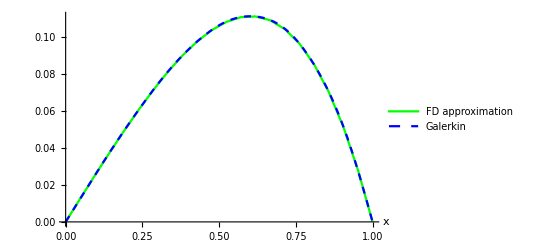

37.359

0.234

```mathematica
Show[pFD,pGAL]
tgal
tfd
```

## 8.2. Piecewise polynomials and FEM

### a) Write a program that solves (5.2), when k(x) = 1 and l = 1 using FEM method with piecewise polynomials of first order and with two different f(x). Compare the approximated solutions with the ones obtained using FD method for elliptic problems.

#### f(x) = (3x+x^2)exp(x)

```mathematica
Clear["Global`*"]
(*FEM*)
t0=TimeUsed[];
n=10;
ax[y_]:=1
fun[y_] := (3y+y^2)Exp[y]
u0= 0;
Deltax=N[1/n];
x[0] = 0;
```

```mathematica
For[ i=1,i≤ n, i++, x[i] = x[i-1]+Deltax]
vlin[ k_,y_] := Simplify[
Piecewise[{{(y-x[k-1])/(x[k]-x[k-1]),x[k-1]≤ y ≤ x[k]},{(x[k+1]-y)/(x[k+1]-x[k]),x[k]≤ y ≤ x[k+1]},{0.,  y < x[k-1]},{0.,  y > x[k+1]}}]
]
vlin[n,y_]:=  Simplify[Piecewise[{{(y-x[n-1])/(x[n]-x[n-1]),x[n-1]≤ y ≤ x[n]},{0.,  y < x[n-1]},{0.,  y > x[n]}}]]
dvlin[j_,y_]=D[vlin[j,y],y];
dvlin[n,y_]=D[vlin[n,y],y];
```

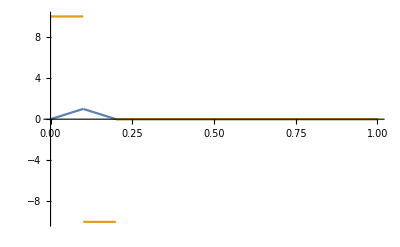

```mathematica
For[ j=1,j≤ n, j++,v[j_,y_] := vlin[j,y]/;  Mod[j,1]==0]
For[ j=1,j≤ n, j++,dv[j_,y_] := dvlin[j,y]/;  Mod[j,1]==0]
Plot[{v [1,y],dv[1,y]},{y,0,1},PlotRange->Full]
```

```mathematica
Do[ a[i,j] = N[∫_0^1 ax[s] dv[j,s]  dv[i,s]ⅆs ],{i,n-1},{j,n-1}]
AA = Table[a[i,j],{i,n-1},{j,n-1}];
MatrixForm[%];
Det[AA];
Do[ b[j] =N[∫_0^1 fun[s] v[j,s]ⅆs ],{j,n-1}]
ff=Array[b,n-1];
MatrixForm[%];
```

```mathematica
(* Solve the system and write the solution. *)
u = N[LinearSolve[AA, ff]];
Solution [y_] := u0 +∑_(k=1)^(n-1) u[[k]] v[k,y];
t1=TimeUsed[];
Print["time FEM"]
tFEM=t1-t0
```

time FEM

2.157

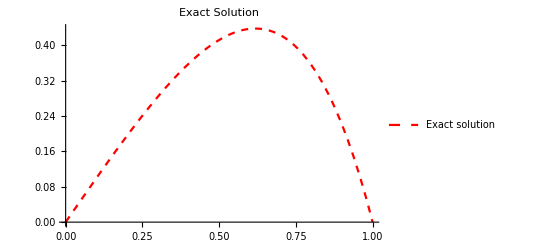

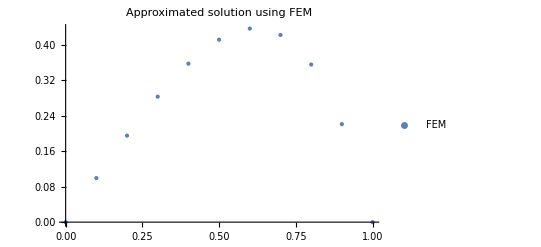

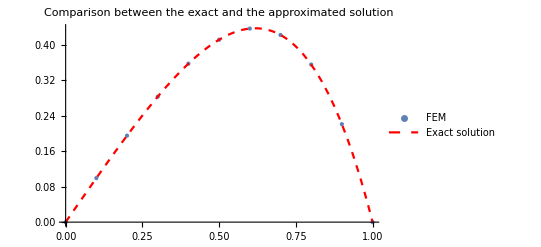

```mathematica
(*plot the exact and approximate solution. *)
Uexact[y_]:=-Exp[y](-1+y)y; 
Plot1=Plot[{Uexact[y]},{y,0,1}, PlotStyle->{Red, {Red, Dashed}}, PlotLabel->"Exact Solution",PlotLegends->{"Exact solution"}]

Plot2=ListPlot[Table[{x[i],Solution[x[i]]},{i,0,n}],PlotStyle->PointSize[Large],PlotLabel->"Approximated solution using FEM",PlotLegends->{"FEM"}]

Show[Plot2,Plot1,PlotLabel->"Comparison between the exact and the approximated solution"]
```

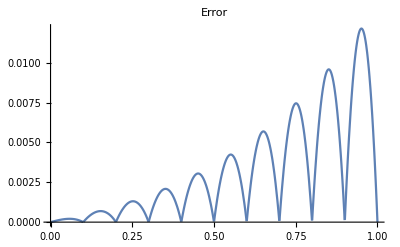

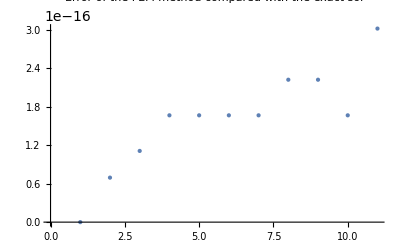

4.44089×10^-16

```mathematica
Plot[{Uexact[y]-Solution[y]},{y,0,1},PlotRange->Full, PlotLabel->"Error"]

DiscreteError[i_]:= Uexact[x[i]]-Solution[x[i]]
ListPlot[Table[DiscreteError[i],{i,0,n}],PlotStyle->PointSize[Medium],PlotLabel->"Error of the FEM method compared with the exact sol"]
Max[Table[Abs[Uexact[y]-Solution[y]],{y,0,1,1/n}]]
```

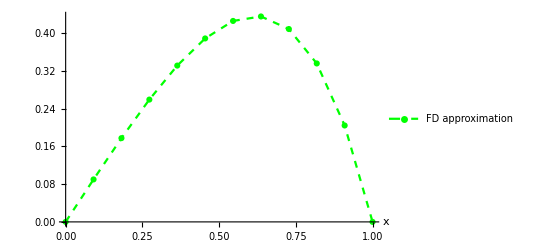

time

0.094

```mathematica
(*approximate solution using FD method for elliptic problem*)
t2=TimeUsed[];
M = 10;
Δx= 1/(M+1);
xx[j_]:= j Δx;
BB:= BB=Table[fun[xx[i]] ,{i,M}]; A:= A=SparseArray[{i_,j_}/;i==j+1->-1,{M,M}] + SparseArray[{i_,j_}/;i==j-1->-1,{M,M}] + SparseArray[{i_,j_}/;i==j->2,{M,M}]//Normal
Anew = A / (Δx^2);
XX=Table[X[j],{j,M}] ; 
Sol1 = Solve[Anew. XX == BB, XX];
XX1 = Flatten[XX /. Sol1];
XX1 = Prepend[XX1,0]; 
XX1 = Append[XX1,0]; 
Plot3=ListPlot[Table[{Δx j, XX1[[j+1]]},{j,0,M+1}], Joined-> True, PlotRange-> All, AxesLabel -> {"x", " "},PlotMarkers->Automatic,PlotStyle->{Green,Dashed,PointSize[Large]},PlotLegends->{"FD approximation"}]
t3=TimeUsed[];
Print["time"]
tFD=t3-t2
```

```mathematica
DiscreteError2[i_]:= Uexact[x[i]]-Sol1[x[i]]
ListPlot[Table[DiscreteError2[i],{i,0,n}],PlotStyle->PointSize[Medium],PlotLabel->"Error of the FD method compared with the exact sol"]
```

-Graphics-

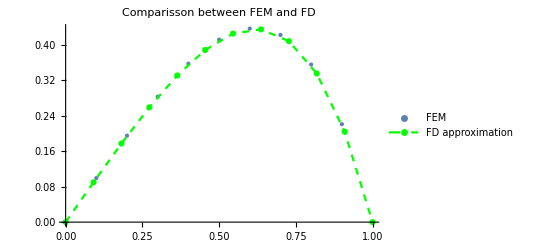

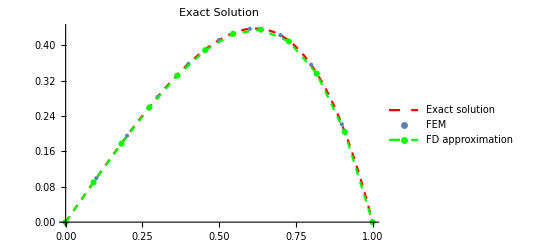

```mathematica
Show[Plot2,Plot3,PlotLabel->"Comparisson between FEM and FD"]
Show[Plot1,Plot2,Plot3]
```

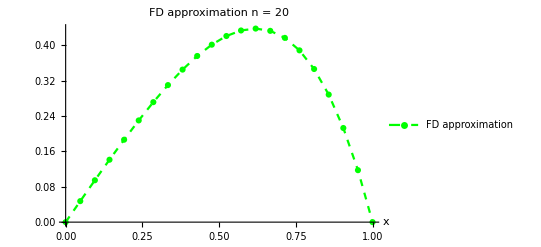

0.156

```mathematica
(*We do FD with n = 20*)
t4=TimeUsed[];
M2 = 20;
Δx2= 1/(M2+1);
xx2[j_]:= j Δx2;
fun2[y_] := (3y+y^2)Exp[y]
BB2:= BB2=Table[fun2[xx2[i]] ,{i,M2}]; A2:= A2=SparseArray[{i_,j_}/;i==j+1->-1,{M2,M2}] + SparseArray[{i_,j_}/;i==j-1->-1,{M2,M2}] + SparseArray[{i_,j_}/;i==j->2,{M2,M2}]//Normal
Anew2 = A2 / (Δx2^2);
XX2=Table[X[j],{j,M2}] ; 
Sol12 = Solve[Anew2. XX2 == BB2, XX2];
XX12 = Flatten[XX2 /. Sol12];
XX12 = Prepend[XX12,0]; 
XX12 = Append[XX12,0]; 
Plot4=ListPlot[Table[{Δx2 j, XX12[[j+1]]},{j,0,M2+1}], Joined-> True, PlotRange-> All, AxesLabel -> {"x", " "},PlotMarkers->Automatic,PlotStyle->{Green,Dashed,PointSize[Large]},PlotLegends->{"FD approximation"},PlotLabel->"FD approximation n = 20"]
t5=TimeUsed[];
time=t5-t4
```

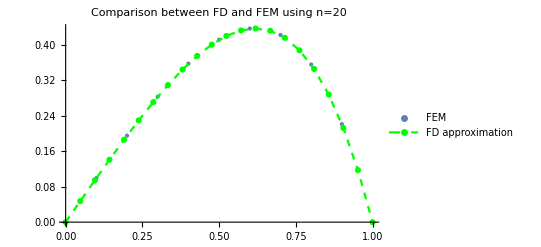

```mathematica
Show[Plot2,Plot4,PlotLabel->"Comparison between FD and FEM using n=20"]
```

#### f(x) = sin(x)exp(x)

```mathematica
Clear["Global`*"]
t0=TimeUsed[];
n=10;
ax[y_]:=1
fun[y_] := Sin[y]Exp[y]
u0= 0;
Deltax=N[1/n];
x[0] = 0;
```

```mathematica
For[ i=1,i≤ n, i++, x[i] = x[i-1]+Deltax]
vlin[ k_,y_] := Simplify[
Piecewise[{{(y-x[k-1])/(x[k]-x[k-1]),x[k-1]≤ y ≤ x[k]},{(x[k+1]-y)/(x[k+1]-x[k]),x[k]≤ y ≤ x[k+1]},{0.,  y < x[k-1]},{0.,  y > x[k+1]}}]
]
vlin[n,y_]:=  Simplify[Piecewise[{{(y-x[n-1])/(x[n]-x[n-1]),x[n-1]≤ y ≤ x[n]},{0.,  y < x[n-1]},{0.,  y > x[n]}}]]
dvlin[j_,y_]=D[vlin[j,y],y];
dvlin[n,y_]=D[vlin[n,y],y];
```

```mathematica
For[ j=1,j≤ n, j++,v[j_,y_] := vlin[j,y]/;  Mod[j,1]==0]
For[ j=1,j≤ n, j++,dv[j_,y_] := dvlin[j,y]/;  Mod[j,1]==0]
Plot[{v [1,y],dv[1,y]},{y,0,1},PlotRange->Full]
Do[ a[i,j] = N[∫_0^1 ax[s] dv[j,s]  dv[i,s]ⅆs ],{i,n-1},{j,n-1}]
AA = Table[a[i,j],{i,n-1},{j,n-1}];
MatrixForm[%];
Det[AA];
Do[ b[j] =N[∫_0^1 fun[s] v[j,s]ⅆs ],{j,n-1}]
ff=Array[b,n-1];
MatrixForm[%];
```

-Graphics-

```mathematica
(* Solve the system and write the solution. *)
u = N[LinearSolve[AA, ff]];
Solution [y_] := u0 +∑_(k=1)^(n-1) u[[k]] v[k,y];
t1=TimeUsed[];
tFEM=t1-t0
```

4.516

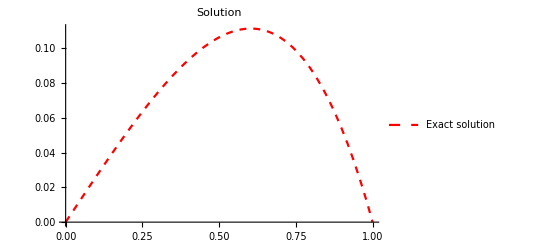

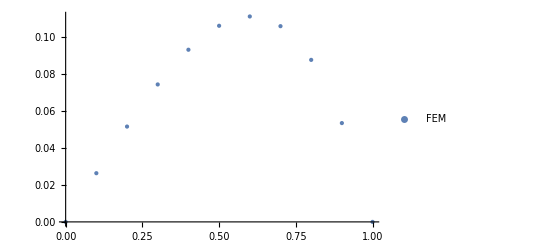

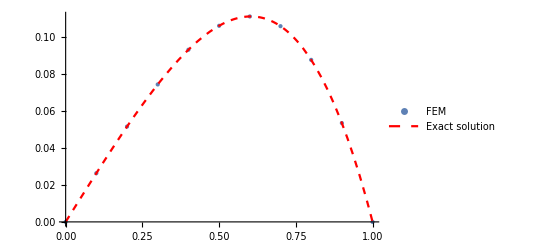

```mathematica
(* Plot the exact and approximate solution. *)
Uexact[y_]:=1/2 (-1+y-ⅇ y Cos[1]+ⅇ^y Cos[y]); 
Plot1=Plot[{Uexact[y]},{y,0,1}, PlotStyle->{Blue, {Red, Dashed}}, PlotLabel->"Solution",PlotLegends->{"Exact solution"}]

Plot2=ListPlot[Table[{x[i],Solution[x[i]]},{i,0,n}],PlotStyle->PointSize[Large],PlotLegends->{"FEM"}]

Show[Plot2,Plot1]
```

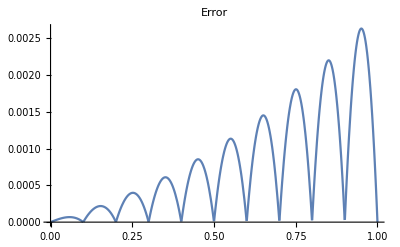

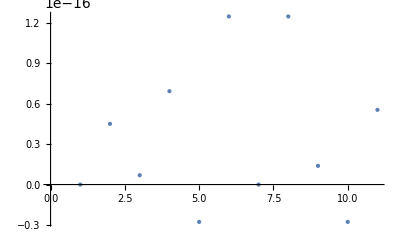

1.66533×10^-16

```mathematica
(*Error*)
Plot[{Uexact[y]-Solution[y]},{y,0,1},PlotRange->Full, PlotLabel->"Error"]

DiscreteError[i_]:= Uexact[x[i]]-Solution[x[i]]
ListPlot[Table[DiscreteError[i],{i,0,n}],PlotStyle->PointSize[Medium]]
Max[Table[Abs[Uexact[y]-Solution[y]],{y,0,1,1/n}]]
```

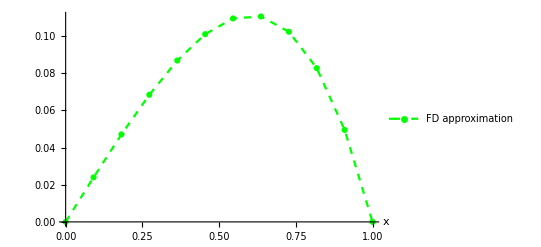

time

0.093

```mathematica
(*approximate solution using FD method for elliptic problem*)
t2=TimeUsed[];
M = 10;
Δx= 1/(M+1);
xx[j_]:= j Δx;
BB:= BB=Table[fun[xx[i]] ,{i,M}]; A:= A=SparseArray[{i_,j_}/;i==j+1->-1,{M,M}] + SparseArray[{i_,j_}/;i==j-1->-1,{M,M}] + SparseArray[{i_,j_}/;i==j->2,{M,M}]//Normal
Anew = A / (Δx^2);
XX=Table[X[j],{j,M}] ; 
Sol1 = Solve[Anew. XX == BB, XX];
XX1 = Flatten[XX /. Sol1];
XX1 = Prepend[XX1,0]; 
XX1 = Append[XX1,0]; 
Plot3=ListPlot[Table[{Δx j, XX1[[j+1]]},{j,0,M+1}], Joined-> True, PlotRange-> All, AxesLabel -> {"x", " "},PlotMarkers->Automatic,PlotStyle->{Green,Dashed,PointSize[Large]},PlotLegends->{"FD approximation"}]
t3=TimeUsed[];
Print["time"]
tFD=t3-t2
```

```mathematica
DiscreteError2[i_]:= Uexact[x[i]]-Sol1[x[i]]
ListPlot[Table[DiscreteError2[i],{i,0,n}],PlotStyle->PointSize[Medium],PlotLabel->"Error of the FD method compared with the exact sol"]
```

-Graphics-

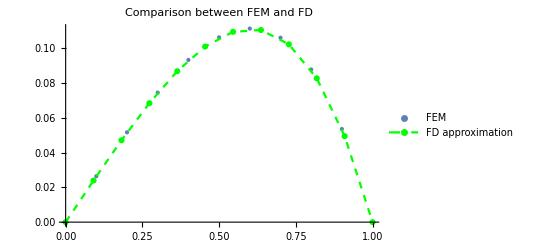

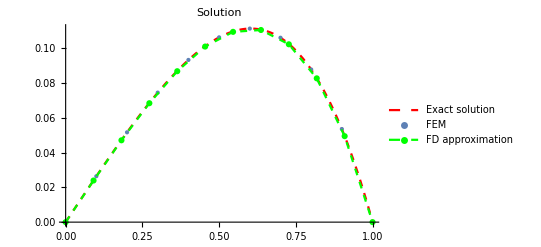

```mathematica
Show[Plot2,Plot3,PlotLabel->"Comparison between FEM and FD"]
Show[Plot1,Plot2,Plot3]
```

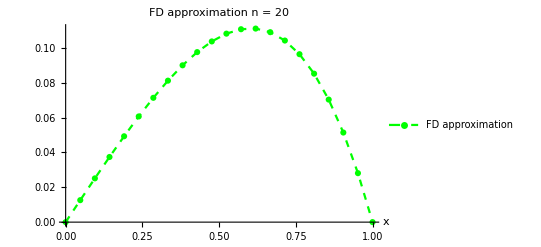

0.266

```mathematica
(*We do FD with n = 20*)
t4=TimeUsed[];
M2 = 20;
Δx2= 1/(M2+1);
xx2[j_]:= j Δx2;
fun2[y_] := Sin[y]Exp[y]
BB2:= BB2=Table[fun2[xx2[i]] ,{i,M2}]; A2:= A2=SparseArray[{i_,j_}/;i==j+1->-1,{M2,M2}] + SparseArray[{i_,j_}/;i==j-1->-1,{M2,M2}] + SparseArray[{i_,j_}/;i==j->2,{M2,M2}]//Normal
Anew2 = A2 / (Δx2^2);
XX2=Table[X[j],{j,M2}] ; 
Sol12 = Solve[Anew2. XX2 == BB2, XX2];
XX12 = Flatten[XX2 /. Sol12];
XX12 = Prepend[XX12,0]; 
XX12 = Append[XX12,0]; 
Plot4=ListPlot[Table[{Δx2 j, XX12[[j+1]]},{j,0,M2+1}], Joined-> True, PlotRange-> All, AxesLabel -> {"x", " "},PlotMarkers->Automatic,PlotStyle->{Green,Dashed,PointSize[Large]},PlotLegends->{"FD approximation"},PlotLabel->"FD approximation n = 20"]
t5=TimeUsed[];
time=t5-t4
```

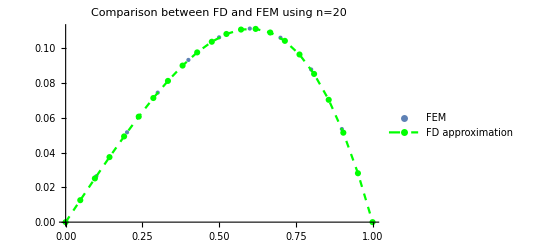

```mathematica
Show[Plot2,Plot4,PlotLabel->"Comparison between FD and FEM using n=20"]
```

## 8.3 Problem with Neumann BC

### a) Write a program in Mathematica that solves (8.10) when k(x) = 1 and l = 1, using FEM method with piecewise polynomials of first order with f(x) = (x^2 + x - 1)*Exp(x), alpha = 0 and betha = 0. Compare the approximate solutions with the one obtained using the DSolve command.

```mathematica
Clear["Global`*"]
n=10;

(* Define the funtions*)
ax[y_]:=1
fun[y_] := (y^2+y-1)*Exp[y]
u0= 0;
```

```mathematica
Δx=N[1/n];
x[0] = 0;
For[ i=1,i≤ n, i++, x[i] = x[i-1]+Δx]
```

```mathematica
vlin[ k_,y_] := Simplify[
Piecewise[{{(y-x[k-1])/(x[k]-x[k-1]),x[k-1]≤ y ≤ x[k]},{(x[k+1]-y)/(x[k+1]-x[k]),x[k]≤ y ≤ x[k+1]},{0.,  y < x[k-1]},{0.,  y > x[k+1]}}]
]
vlin[n,y_]:=  Simplify[Piecewise[{{(y-x[n-1])/(x[n]-x[n-1]),x[n-1]≤ y ≤ x[n]},{0.,  y < x[n-1]},{0.,  y > x[n]}}]]
vlin[0,y_]=  Simplify[Piecewise[{{(x[1]-y)/(x[1]-x[0]),x[0]≤ y ≤ x[1]},{0.,  y < x[0]},{0.,  y > x[0]}}]]
dvlin[j_,y_]=D[vlin[j,y],y];
dvlin[n,y_]=D[vlin[n,y],y];
dvlin[0,y_]=D[vlin[0,y],y];
```

```mathematica
For[ j=1,j≤ n, j++,v[j_,y_] := vlin[j,y]/;  Mod[j,1]==0]
For[ j=1,j≤ n, j++,dv[j_,y_] := dvlin[j,y]/;  Mod[j,1]==0]
Plot[{v [1,y],dv[1,y]},{y,0,1},PlotRange->Full]
```

```mathematica
Do[ a[i,j] = N[∫_0^1 ax[s] dv[j,s]  dv[i,s]ⅆs ],{i,0,n-1},{j,0,n-1}]
AA = Table[a[i,j],{i,0,n-1},{j,0,n-1}];
MatrixForm[%];
Det[AA];
Do[ b[j] =N[∫_0^1 fun[s] v[j,s]ⅆs ],{j,0,n-1}]
ff= Table[b[j],{j,0,n-1}];
MatrixForm[%];

(* Solve the system and write the solution. *)
u = N[LinearSolve[AA, ff]];
Solution [y_] := ∑_(k=0)^(n-1) u[[k+1]] v[k,y];
```

```mathematica
gFEM=ListPlot[Table[{x[i],Solution[x[i]]},{i,0,n}],PlotStyle->{Blue,PointSize[Large]},PlotLegends->{"FEM"}]
```

We calculate and plot the exact solution

```mathematica
DSolve[{-ax'[x]*u1'[x]-ax[x]*u1''[x]==fun[x],u1'[0]==0,u1'[1]==0,u1[1]==0},u1[x],x](*We calculate the exact solution*)
```

```mathematica
Uexact[x_]:=ⅇ-3 ⅇ^x+3 ⅇ^x x-ⅇ^x x^2
```

```mathematica
gEX=Plot[Evaluate[Uexact[x]],{x,0,1},PlotStyle->Green,PlotLegends->{"exact solution"}]
```

```mathematica
Show[gEX,gFEM]
```

We compute the discrete error

```mathematica
DiscreteError[i_]:= Uexact[x[i]]-Solution[x[i]]
ListPlot[Table[DiscreteError[i],{i,0,n}],PlotStyle->PointSize[Large]]
```

```mathematica
Max[Table[Abs[DiscreteError[i]],{i,0,n}]]
```